# 1. kviz - Računalniška orodja v matematiki

Na kvizu je skupno možno doseči 20 točk. Za vsako pravilno rešeno podnalogo dobite 1 točko. Delnih točk ni.
Rešitve pišite takoj pod navodilom ustrezne podnaloge. 

Veliko uspeha pri reševanju!

#### 1. Prepisovalna pravila

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja s klicem funkcije f na argumentu x.

```mathematica
pravilo=x_:>f[x]
```

x_:>f[x]

b. Na izrazu `izraz` najprej uporabite pravilo definirano v prejšnji nalogi za funkcijo , nato pa s prepisovalnimi pravili izračunajte vrednost dobljenega izraza za x = e (x = ⅇ) in y = 1/2.

```mathematica
izraz = Log[x] + 2y / x;
noviIzraz=izraz/. pravilo
rezultat=noviIzraz/. {x->E,y->1/2}
```

1+((2 y)/x+Log[x])^4

1+(1+1/ⅇ)^4

c. Definirajte prepisovalno pravilo, ki zamenja vse pojavitve  z .

```mathematica
pravilo2 = x^n_ -> x^(n+1)/(2n + 1)
```

x^n_→x^(1+n)/(1+2 n)

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
g[x_]:= x^(-42)
g[x]//.pravilo2
```

1/536347102817482913555411512425352545980058003572241486357421875

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`.

```mathematica
Fib[n_]:= Nest[Replace[{x_, y_}-> {y, x+y}], {0,1}, n][[1]]
Fib[10]
```

55

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
ClearAll[g, f, x, y]
```

b. Definirajte tabelo, ki bo vsebovala numerične približke naravnega logaritma v vseh številih med 1 in 100.

```mathematica
log = Table[N[Log[x], 4], {x, 1, 100}]
```

{0,0.6931,1.099,1.386,1.609,1.792,1.946,2.079,2.197,2.303,2.398,2.485,2.565,2.639,2.708,2.773,2.833,2.89,2.944,2.996,3.045,3.091,3.135,3.178,3.219,3.258,3.296,3.332,3.367,3.401,3.434,3.466,3.497,3.526,3.555,3.584,3.611,3.638,3.664,3.689,3.714,3.738,3.761,3.784,3.807,3.829,3.85,3.871,3.892,3.912,3.932,3.951,3.97,3.989,4.007,4.025,4.043,4.06,4.078,4.094,4.111,4.127,4.143,4.159,4.174,4.19,4.205,4.22,4.234,4.248,4.263,4.277,4.29,4.304,4.317,4.331,4.344,4.357,4.369,4.382,4.394,4.407,4.419,4.431,4.443,4.454,4.466,4.477,4.489,4.5,4.511,4.522,4.533,4.543,4.554,4.564,4.575,4.585,4.595,4.605}

c.  Iz tabele v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu desetin (prvo decimalno mesto) praštevilo.

```mathematica
prast= Select[log, PrimeQ[Mod[Floor[#*10],10]]&]
```

{1.386,1.792,2.303,2.398,2.565,2.708,2.773,3.219,3.258,3.296,3.332,3.367,3.526,3.555,3.584,3.714,3.738,3.761,3.784,4.205,4.22,4.234,4.248,4.263,4.277,4.29,4.304,4.317,4.331,4.344,4.357,4.369,4.382,4.394,4.511,4.522,4.533,4.543,4.554,4.564,4.575,4.585,4.595}

d. Definirajte anonimno funkcijo enega argumenta, ki  izračuna kub argumenta in prišteje argument in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
anonimna = (#^3 + #)&;
novo = anonimna/@prast
```

{4.05,7.54,14.5,16.2,19.4,22.6,24.1,36.6,37.8,39.1,40.3,41.5,47.4,48.5,49.6,54.9,56.,57.,58.,78.5,79.3,80.1,80.9,81.7,82.5,83.3,84.,84.8,85.6,86.3,87.1,87.8,88.5,89.3,96.3,97.,97.7,98.3,99.,99.7,100.,101.,102.}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so soda.

```mathematica
zaokrozeno= Floor[novo];
sode=Select[zaokrozeno,EvenQ];
vsota=Total[sode]
```

1564

#### 3. Analiza z mathematico

a. Definirajte funkcijo .

```mathematica
f[x_]:=5 Exp[x] x^2
```

b. Izračunajte definicijsko območje funkcije .

```mathematica
FunctionDomain[f[x], x]
```

True

c. Izračunajte zalogo vrednosti funkcije .

```mathematica
FunctionRange[f[x], x, y]
```

y≥0

d. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x], x -> Infinity]
```

∞

```mathematica
Limit[f[x], x -> -Infinity]
```

0

e. Izračunajte odvod funkcije .

```mathematica
odvod = D[f[x], x]
```

10 ⅇ^x x+5 ⅇ^x x^2

f. Izračunajte lokalne ekstreme funkcije  (določi tudi ali gre za lokalni minimum oz. maksimum).

```mathematica
drugiodvod = D[f[x], {x, 2}]
```

10 ⅇ^x+20 ⅇ^x x+5 ⅇ^x x^2

```mathematica
Map[{#, f[#]}&, Solve[odvod == 0, x] // Flatten // Values]
```

{{-2,20/ⅇ^2},{0,0}}

```mathematica
(*minimum*)
```

```mathematica
drugiodvod /. {x -> -2}
```

-10/ⅇ^2

```mathematica
(*maksimum*)
drugiodvod /. {x -> 0}
```

10

g. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
(*narašča*)
```

```mathematica
Reduce[odvod >= 0, x]
```

x≤-2||x≥0

```mathematica
(*pada*)
Reduce[odvod <= 0, x]
```

-2≤x≤0

h. Narišite graf funkcije  na intervalu [-1, 2].

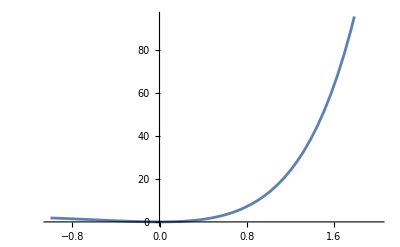

```mathematica
Plot[f[x], {x, -1, 2}]
```

i. Določite intervale konveksnosti in konkavnosti funkcije .

```mathematica
(*konveksno*)
Reduce[drugiodvod >= 0, x]
```

x≤-2-√2||x≥-2+√2

```mathematica
(*konkavno*)
Reduce[drugiodvod <= 0, x]
```

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [-3, 0]. Vrtenino tudi narišite.

```mathematica
Integrate[2 Pi x(f[x]), {x,-3,0}]
RevolutionPlot3D[f[x],{x,-3,0},RevolutionAxis->{1, 0, 0}]
```

10 (-6+78/ⅇ^3) π

-Graphics3D-